```mathematica
ClearAll["Global`*"]
mh2=2.01533
mh=1.00794
mp=1.00728
mu1=1/(1/mp+1/mh2)
mu2=1/(1/mp+1/mh)
```

2.01533

1.00794

1.00728

0.671606

0.503805

1.

2.56128 y

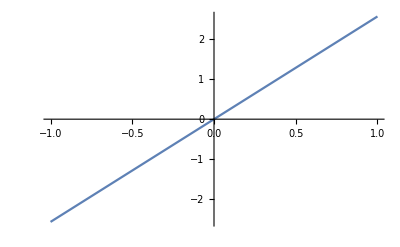

-2.56128 Cos[y] Sin[y]

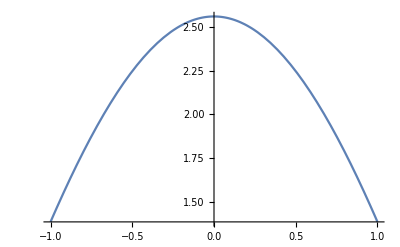

```mathematica
ClearAll["Global`*"]
c=17.283;
a=2.027;
B=0.375;
R=1.
V[r_,R_,y_]:=c Exp[-a R](1+B/2(3 y^2-1))
dv[y_]=D[V[r,R,y],y]
Plot[dv[y],{y,-1,1}]
V[r_,R_,y_]:=c Exp[-a R](1+B/2(3 Cos[y]^2-1))
dv[y_]=D[V[r,R,y],y]
Plot[-1/Sin[y]dv[y],{y,-1, 1}]
```

```mathematica
f[r_,R_,y_]:=1/Norm[r]-1/Norm[R+r/2+.1]-1/Norm[R-r/2+.1]
R1={1,0,0};
z=0;
R2={x,y,z};
range=2;
f[R1,R2,1]
Plot3D[f[R1,R2,1],{x,-range,range},{y,-range,range},PlotRange->All]
```

1-1/(√(0.01+Abs[-0.4+x]^2+Abs[0.1+y]^2))-1/(√(0.01+Abs[0.6+x]^2+Abs[0.1+y]^2))

-Graphics3D-

```mathematica
z=0;
R1={x,y,z};
R2={0,1,0};
range=4;
f[R1,R2,1]
Plot3D[f[R1,R2,1],{x,-range,range},{y,-range,range}]
```

-1/(√(0.01+Abs[0.1-x/2]^2+Abs[1.1-y/2]^2))-1/(√(0.01+Abs[0.1+x/2]^2+Abs[1.1+y/2]^2))+1/(√(Abs[x]^2+Abs[y]^2))

-Graphics3D-

```mathematica
ClearAll["Global`*"]
a=ArcTan[y]
```

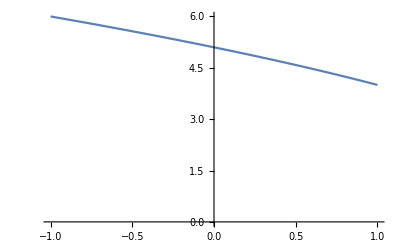

```mathematica
r=2;
R=5;
Plot[Sqrt[R^2-r R x + r^2/4],{x,1,-1},PlotRange->{{-1,1},{0,6}}]
```

```mathematica
ClearAll["Global`*"]
f[r_,R_,cosGamma_]:=1/r-1/Sqrt[R^2-2R r cosGamma+(r/2)^2]-1/Sqrt[R^2+2R r cosGamma+(r/2)^2];
range=5
Plot3D[f[r,R,0],{r,1,range},{R,0,range}]
```

```mathematica
ClearAll["Global`*"]
alpha=1. 10^-6;
f[r_,R_,y_]:=1/(r+alpha)-1/(Sqrt[r^2/4+R^2-r R y]+alpha)-1/(Sqrt[r^2/4+R^2+r R y]+alpha)
Plot3D[f[r,R,0.0101],{R,0,10},{r,1,10},PlotRange->{{0,10},{1,10},{-5,1}}]
Plot3D[f[2.82,R,y],{R,0,10},{y,-1,1},PlotRange->{{0,10},{-1,1},{-5,1}}]
Plot3D[f[r,0,y],{r,1,10},{y,-1.0,1},PlotRange->{{0,10},{-1,1},{-5,1}}]
r1=Table[i,{i,0,10,1}]
r2=Table[i,{i,0,10,1}]
y1=Table[i,{i,-1,1,0.2}]
Table[f[r1[[i]],r2[[i]],y1[[i]]],{i,1,11}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

{0,1,2,3,4,5,6,7,8,9,10}

{0,1,2,3,4,5,6,7,8,9,10}

{-1.,-0.8,-0.6,-0.4,-0.2,0.,0.2,0.4,0.6,0.8,1.}

{-1.×10^6,-1.18914,-0.487781,-0.287717,-0.201589,-0.157771,-0.134392,-0.123307,-0.121945,-0.132127,-0.166667}

-Graphics3D-

```mathematica
r={rx,ry,rz}
R={Rx,Ry,Rz}
D[ArcCos[r . R/(Norm[r]Norm[R])],{r}]
```

{rx,ry,rz}

{Rx,Ry,Rz}

{-(Rx/(√(Abs[rx]^2+Abs[ry]^2+Abs[rz]^2) √(Abs[Rx]^2+Abs[Ry]^2+Abs[Rz]^2))-((rx Rx+ry Ry+rz Rz) Abs[rx] Abs'[rx])/((Abs[rx]^2+Abs[ry]^2+Abs[rz]^2)^(3/2) √(Abs[Rx]^2+Abs[Ry]^2+Abs[Rz]^2)))/(√(1-(rx Rx+ry Ry+rz Rz)^2/((Abs[rx]^2+Abs[ry]^2+Abs[rz]^2) (Abs[Rx]^2+Abs[Ry]^2+Abs[Rz]^2)))),-(Ry/(√(Abs[rx]^2+Abs[ry]^2+Abs[rz]^2) √(Abs[Rx]^2+Abs[Ry]^2+Abs[Rz]^2))-((rx Rx+ry Ry+rz Rz) Abs[ry] Abs'[ry])/((Abs[rx]^2+Abs[ry]^2+Abs[rz]^2)^(3/2) √(Abs[Rx]^2+Abs[Ry]^2+Abs[Rz]^2)))/(√(1-(rx Rx+ry Ry+rz Rz)^2/((Abs[rx]^2+Abs[ry]^2+Abs[rz]^2) (Abs[Rx]^2+Abs[Ry]^2+Abs[Rz]^2)))),-(Rz/(√(Abs[rx]^2+Abs[ry]^2+Abs[rz]^2) √(Abs[Rx]^2+Abs[Ry]^2+Abs[Rz]^2))-((rx Rx+ry Ry+rz Rz) Abs[rz] Abs'[rz])/((Abs[rx]^2+Abs[ry]^2+Abs[rz]^2)^(3/2) √(Abs[Rx]^2+Abs[Ry]^2+Abs[Rz]^2)))/(√(1-(rx Rx+ry Ry+rz Rz)^2/((Abs[rx]^2+Abs[ry]^2+Abs[rz]^2) (Abs[Rx]^2+Abs[Ry]^2+Abs[Rz]^2))))}

```mathematica
ClearAll["Global`*"]
D[ArcCos[r R/(Norm[r]Norm[R])],r]
```

-(R/(Norm[r] Norm[R])-(r R Norm'[r])/(Norm[r]^2 Norm[R]))/(√(1-(r^2 R^2)/(Norm[r]^2 Norm[R]^2)))